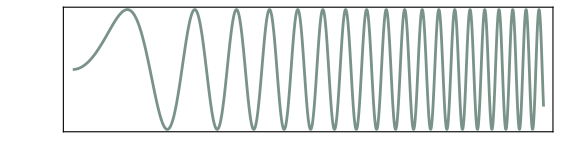

```mathematica
LogLinearPlot[Sin[.05 Log[x]^2],{x,10^0,10^21},PlotRange->All,AspectRatio->.25,Frame->True,PlotStyle->Thickness[.0035],ImageSize->Large,ColorFunction->Function[{x,y},ColorData["Rainbow"][Floor[5 Log[x]/21] /15]],FrameTicks->{None,None},Axes->False,ColorFunctionScaling->False,PerformanceGoal->"Quality",PlotLegends->Placed[BarLegend[{"Rainbow",{0,1}},5],Below]]
```